```mathematica
Unprotect[$ProcessorCount];$ProcessorCount=4;
```

```mathematica
R0=6356.766`30;
ZtoH[Z_]=(Z R0)/(Z+R0);
HtoZ[H_]=(H R0)/(R0-H);
```

```mathematica
Hb={0,11,20,32,47,51,71,ZtoH[86]};
Zb = {0,HtoZ[Hb[[2]]],HtoZ[Hb[[3]]],HtoZ[Hb[[4]]],HtoZ[Hb[[5]]],HtoZ[Hb[[6]]],HtoZ[Hb[[7]]],86,91,110,120,1000};
Lb={-6.5`30,0,1,2.8`30,0,-2.8`30,-2,0,0,12,0,0};
Zcorr=Table[z,{z,80,86,1/2}];
Mcorr={1,0.999996`30,0.999989`30,0.999971`30,0.999941`30,0.999909`30,0.999870`30,0.999829`30,0.999786`30,0.999741`30,0.999694`30,0.999641`30,0.9995788`30};
Tinf=1000;
```

```mathematica
Tb={288.15`30,0,0,0,0,0,0,0,0,0,0,0};
b=2;
Tb[[b]]=Tb[[b-1]]+Lb[[b-1]](Hb[[b]]-Hb[[b-1]]);
b=3;
Tb[[b]]=Tb[[b-1]]+Lb[[b-1]](Hb[[b]]-Hb[[b-1]]);
b=4;
Tb[[b]]=Tb[[b-1]]+Lb[[b-1]](Hb[[b]]-Hb[[b-1]]);
b=5;
Tb[[b]]=Tb[[b-1]]+Lb[[b-1]](Hb[[b]]-Hb[[b-1]]);
b=6;
Tb[[b]]=Tb[[b-1]]+Lb[[b-1]](Hb[[b]]-Hb[[b-1]]);
b=7;
Tb[[b]]=Tb[[b-1]]+Lb[[b-1]](Hb[[b]]-Hb[[b-1]]);
b=8;
Tb[[b]]=(Tb[[b-1]]+Lb[[b-1]](Hb[[b]]-Hb[[b-1]]))Mcorr[[-1]];
b=9;
Tb[[b]]=Tb[[b-1]]+Lb[[b-1]](Zb[[b]]-Zb[[b-1]]);
b=10;
Tb[[b]]=240;
b=11;
Tb[[b]]=Tb[[b-1]]+Lb[[b-1]](Zb[[b]]-Zb[[b-1]]);
b=12;
Tb[[b]]=Tinf;
Tb//TableForm
```

288.15
216.65
216.65
228.65
270.65
270.65
214.65
186.86716669360826079978692382
186.86716669360826079978692382
240
360
1000

```mathematica
Tc=(Lb[[10]](Zb[[10]]-Zb[[9]])Tb[[10]]+Tb[[9]]^2-Tb[[10]]^2)/(Lb[[10]](Zb[[10]]-Zb[[9]])+2Tb[[9]]-2Tb[[10]])
bigA=Tb[[9]]-Tc
littleA=((Zb[[10]]-Zb[[9]])bigA)/(√(bigA^2-(Tb[[10]]-Tc)^2))
λ=N[Lb[[10]]/(Tinf-Tb[[11]])]
```

263.1906471790912887537992211

-76.3234804854830279540122973

-19.9428815545855327095184745

0.01875

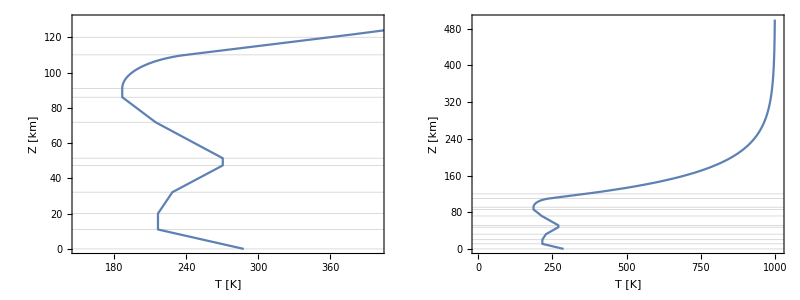

```mathematica
T[Z_]=Piecewise[{
{Tb[[1]]+Lb[[1]](ZtoH[Z]-Hb[[1]]),Zb[[1]]≤Z<Zb[[2]]},
{Tb[[2]],Zb[[2]]≤Z≤Zb[[3]]},
{Tb[[3]]+Lb[[3]](ZtoH[Z]-Hb[[3]]),Zb[[3]]<Z≤Zb[[4]]},
{Tb[[4]]+Lb[[4]](ZtoH[Z]-Hb[[4]]),Zb[[4]]<Z<Zb[[5]]},
{Tb[[5]],Zb[[5]]≤Z≤Zb[[6]]},
{Tb[[6]]+Lb[[6]](ZtoH[Z]-Hb[[6]]),Zb[[6]]<Z≤Zb[[7]]},
{Piecewise[{
{Tb[[7]]+Lb[[7]](ZtoH[Z]-Hb[[7]]),Zb[[7]]<Z≤Zcorr[[1]]},
{(Tb[[7]]+Lb[[7]](ZtoH[Z]-Hb[[7]]))(Mcorr[[1]]+((Mcorr[[2]]-Mcorr[[1]])(Z-Zcorr[[1]]))/(Zcorr[[2]]-Zcorr[[1]])),Zcorr[[1]]<Z≤Zcorr[[2]]},
{(Tb[[7]]+Lb[[7]](ZtoH[Z]-Hb[[7]]))(Mcorr[[2]]+((Mcorr[[3]]-Mcorr[[2]])(Z-Zcorr[[2]]))/(Zcorr[[3]]-Zcorr[[2]])),Zcorr[[2]]<Z≤Zcorr[[3]]},
{(Tb[[7]]+Lb[[7]](ZtoH[Z]-Hb[[7]]))(Mcorr[[3]]+((Mcorr[[4]]-Mcorr[[3]])(Z-Zcorr[[3]]))/(Zcorr[[4]]-Zcorr[[3]])),Zcorr[[3]]<Z≤Zcorr[[4]]},
{(Tb[[7]]+Lb[[7]](ZtoH[Z]-Hb[[7]]))(Mcorr[[4]]+((Mcorr[[5]]-Mcorr[[4]])(Z-Zcorr[[4]]))/(Zcorr[[5]]-Zcorr[[4]])),Zcorr[[4]]<Z≤Zcorr[[5]]},
{(Tb[[7]]+Lb[[7]](ZtoH[Z]-Hb[[7]]))(Mcorr[[5]]+((Mcorr[[6]]-Mcorr[[5]])(Z-Zcorr[[5]]))/(Zcorr[[6]]-Zcorr[[5]])),Zcorr[[5]]<Z≤Zcorr[[6]]},
{(Tb[[7]]+Lb[[7]](ZtoH[Z]-Hb[[7]]))(Mcorr[[6]]+((Mcorr[[7]]-Mcorr[[6]])(Z-Zcorr[[6]]))/(Zcorr[[7]]-Zcorr[[6]])),Zcorr[[6]]<Z≤Zcorr[[7]]},
{(Tb[[7]]+Lb[[7]](ZtoH[Z]-Hb[[7]]))(Mcorr[[7]]+((Mcorr[[8]]-Mcorr[[7]])(Z-Zcorr[[7]]))/(Zcorr[[8]]-Zcorr[[7]])),Zcorr[[7]]<Z≤Zcorr[[8]]},
{(Tb[[7]]+Lb[[7]](ZtoH[Z]-Hb[[7]]))(Mcorr[[8]]+((Mcorr[[9]]-Mcorr[[8]])(Z-Zcorr[[8]]))/(Zcorr[[9]]-Zcorr[[8]])),Zcorr[[8]]<Z≤Zcorr[[9]]},
{(Tb[[7]]+Lb[[7]](ZtoH[Z]-Hb[[7]]))(Mcorr[[9]]+((Mcorr[[10]]-Mcorr[[9]])(Z-Zcorr[[9]]))/(Zcorr[[10]]-Zcorr[[9]])),Zcorr[[9]]<Z≤Zcorr[[10]]},
{(Tb[[7]]+Lb[[7]](ZtoH[Z]-Hb[[7]]))(Mcorr[[10]]+((Mcorr[[11]]-Mcorr[[10]])(Z-Zcorr[[10]]))/(Zcorr[[11]]-Zcorr[[10]])),Zcorr[[10]]<Z≤Zcorr[[11]]},
{(Tb[[7]]+Lb[[7]](ZtoH[Z]-Hb[[7]]))(Mcorr[[11]]+((Mcorr[[12]]-Mcorr[[11]])(Z-Zcorr[[11]]))/(Zcorr[[12]]-Zcorr[[11]])),Zcorr[[11]]<Z≤Zcorr[[12]]},
{(Tb[[7]]+Lb[[7]](ZtoH[Z]-Hb[[7]]))(Mcorr[[12]]+((Mcorr[[13]]-Mcorr[[12]])(Z-Zcorr[[12]]))/(Zcorr[[13]]-Zcorr[[12]])),Zcorr[[12]]<Z≤Zcorr[[13]]}
}],Zb[[7]]<Z≤Zb[[8]]},
{Tb[[8]],Zb[[8]]<Z≤Zb[[9]]},
{Tc+bigA √(1-((Z-Zb[[9]])/littleA)^2),Zb[[9]]<Z≤Zb[[10]]},
{Tb[[10]]+Lb[[10]](Z-Zb[[10]]),Zb[[10]]<Z≤Zb[[11]]},
{Tinf-(Tinf-Tb[[11]])ⅇ^(-(Lb[[10]]/(Tinf-Tb[[11]]))(((Z-Zb[[11]])(R0+Zb[[11]]))/(R0+Z))),Zb[[11]]<Z≤Zb[[12]]}
}];
Grid[{{
ParametricPlot[{T[Z],Z},{Z,0,130},PlotRange->{{150,400},{0,130}},AspectRatio->1.5,ImageSize->Medium,Exclusions->None,Frame->True,FrameLabel->{"T [K]","Z [km]"},GridLines->{None,Partition[Riffle[Zb,{{Dashed,Thin}}],2]}],
ParametricPlot[{T[Z],Z},{Z,0,500},PlotRange->{{0,1010},{0,500}},AspectRatio->1.5,ImageSize->Medium,Exclusions->None,Frame->True,FrameLabel->{"T [K]","Z [km]"},GridLines->{None,Partition[Riffle[Zb,{{Dashed,Thin}}],2]}]
}}]
```

```mathematica
Pb={101325,0,0,0,0,0,0,0};
g0=9.80665`30;
M0=28.964425912034`30;
R=8.31432`30;
Na=6.022169`30 10^26;
b=2;
Pb[[b]]=Pb[[b-1]](Tb[[b-1]]/Tb[[b]])^((g0 M0)/(R Lb[[b-1]]));
b=3;
Pb[[b]]=Pb[[b-1]] ⅇ^(-(g0 M0(Hb[[b]]-Hb[[b-1]]))/(R Tb[[b-1]]));
b=4;
Pb[[b]]=Pb[[b-1]](Tb[[b-1]]/Tb[[b]])^((g0 M0)/(R Lb[[b-1]]));
b=5;
Pb[[b]]=Pb[[b-1]](Tb[[b-1]]/Tb[[b]])^((g0 M0)/(R Lb[[b-1]]));
b=6;
Pb[[b]]=Pb[[b-1]] ⅇ^(-(g0 M0 (Hb[[b]]-Hb[[b-1]]))/(R Tb[[b-1]]));
b=7;
Pb[[b]]=Pb[[b-1]](Tb[[b-1]]/Tb[[b]])^((g0 M0)/(R Lb[[b-1]]));
b=8;
Pb[[b]]=Pb[[b-1]](Tb[[b-1]]/Tb[[b]])^((g0 M0)/(R Lb[[b-1]]));Pb//TableForm
```

101325
22632.03362389728402750167814
5474.874376757307085858952942
868.014988510785148131379345
110.90562914370221282848871
66.9384346263881217464974074
3.95638449983647254755145701
0.370699003145549604158616946

```mathematica
P[Z_]=Piecewise[{
{Pb[[1]](Tb[[1]]/T[Z])^((g0 M0)/(R Lb[[1]])),Zb[[1]]≤Z≤Zb[[2]]},
{Pb[[2]] ⅇ^(-(g0 M0 (ZtoH[Z]-Hb[[2]]))/(R Tb[[2]])),Zb[[2]]<Z≤Zb[[3]]},
{Pb[[3]](Tb[[3]]/T[Z])^((g0 M0)/(R Lb[[3]])),Zb[[3]]<Z≤Zb[[4]]},
{Pb[[4]](Tb[[4]]/T[Z])^((g0 M0)/(R Lb[[4]])),Zb[[4]]<Z≤Zb[[5]]},
{Pb[[5]] ⅇ^(-(g0 M0(ZtoH[Z]-Hb[[5]]))/(R Tb[[5]])),Zb[[5]]<Z≤Zb[[6]]},
{Pb[[6]](Tb[[6]]/T[Z])^((g0 M0)/(R Lb[[6]])),Zb[[6]]<Z≤Zb[[7]]},
{Pb[[7]](Tb[[7]]/T[Z])^((g0 M0)/(R Lb[[7]])),Zb[[7]]<Z≤Zb[[8]]}
}];
ρP[Z_]=(P[Z]M0)/(R T[Z]);
```

```mathematica
n7={1.129794`30 10^20,8.6`30 10^16,3.030898`30 10^19,1.351400`30 10^18,7.5817`30 10^14};
Mi={28.0134`30,15.9994`30,31.9988`30,39.948`30,4.0026`30,1.00794`30};
g[Z_]=g0(R0/(R0+Z))^2;
dTdZ[Z_]=D[T[Z],Z];
K7=1.2`30 10^2;
K[Z_]=Piecewise[{{K7,Z<95},{K7 ⅇ^(1-400/(400-(Z-95)^2)),95≤Z<115},{0,Z≥115}}];
a={0,6.986`30 10^20,4.863`30 10^20,4.487`30 10^20,1.700`30 10^21,3.305`30 10^21};
b={0,0.750`30,0.750`30,0.870`30,0.691`30,0.500`30};
α={0,0,0,0,-0.40`30,-0.25`30};
Q={0,-5.809644`30 10^-4,1.366212`30 10^-4,9.434079`30 10^-5,-2.457369`30 10^-4};
U={0,56.90311`30,86,86,86};
W={0,2.706240`30 10^-5,8.333333`30 10^-5,8.333333`30 10^-5,6.666667`30 10^-4};
q={0,-3.416248`30 10^-3,0,0,0};
u={0,97,0,0,0};
w={0,5.008765`30 10^-4,0,0,0};
```

```mathematica
pH=1;
pArHe=3;
pO1O2=6;
pN2=9;
wp=30;
```

```mathematica
nN2integrand[z_]=Piecewise[{{(M0 g[z])/(R T[z]),z≤100},{(Mi[[1]] g[z])/(R T[z]),z>100}}];
nN2int[Z_?NumericQ]:=NIntegrate[nN2integrand[z],{z,Zb[[8]],Z},PrecisionGoal->pN2,WorkingPrecision->wp];
nN2[Z_]=n7[[1]] Tb[[8]]/T[Z] ⅇ^(-nN2int[Z]);
```

```mathematica
zBreaks={86,91,110,120,100};
ParallelTable[{zBreaks[[i]],NIntegrate[nN2integrand[z],{z,Zb[[8]],zBreaks[[i]]},PrecisionGoal->pN2,WorkingPrecision->wp]},{i,1,Length[zBreaks]},Method->"FinestGrained"]//TableForm
```

86 | 0.
91 | 0.889173871236893582240386460162
110 | 3.98159977280184761030419504377
120 | 5.05881956915727384772569393723
100 | 2.46393904091324856511317062715

```mathematica
D2[Z_?NumericQ]:=a[[2]]/nN2[Z](T[Z]/(273.15`30))^b[[2]]
nO1integrand[z_]=Piecewise[{
{g[z]/(R T[z])D2[z]/(D2[z]+K[z])(Mi[[2]]+(M0 K[z])/D2[z])+Q[[2]](z-U[[2]])^2 ⅇ^(-W[[2]](z-U[[2]])^3)+q[[2]](u[[2]]-z)^2 ⅇ^(-w[[2]](u[[2]]-z)^3),86≤z≤97},
{g[z]/(R T[z])D2[z]/(D2[z]+K[z])(Mi[[2]]+(M0 K[z])/D2[z])+Q[[2]](z-U[[2]])^2 ⅇ^(-W[[2]](z-U[[2]])^3),97<z≤100},
{g[z]/(R T[z])D2[z]/(D2[z]+K[z])(Mi[[2]]+(Mi[[1]] K[z])/D2[z])+Q[[2]](z-U[[2]])^2 ⅇ^(-W[[2]](z-U[[2]])^3),100<z<115},
{g[z]/(R T[z])Mi[[2]]+Q[[2]](z-U[[2]])^2 ⅇ^(-W[[2]](z-U[[2]])^3),z≥115}
}];
nO1int[Z_?NumericQ]:=NIntegrate[nO1integrand[z],{z,Zb[[8]],Z},PrecisionGoal->pO1O2,WorkingPrecision->wp]
nO1[Z_]:=n7[[2]] Tb[[8]]/T[Z] ⅇ^(-nO1int[Z])
```

```mathematica
zBreaks={91,95,97,100,110,115,120};
ParallelTable[{zBreaks[[i]],NIntegrate[nO1integrand[z],{z,Zb[[8]],zBreaks[[i]]},PrecisionGoal->pO1O2,WorkingPrecision->wp]},{i,1,Length[zBreaks]},Method->"FinestGrained"]//TableForm
```

91 | -1.23351587855320247373287035938
95 | -1.63262275724009664583921376986
97 | -1.67363965069362953358173204834
100 | -1.65195052017487173678349362633
110 | -1.23504039221057066954949918276
115 | -0.980149724011647566367870576137
120 | -0.731233873883614046583901354471

```mathematica
D3[Z_?NumericQ]:=a[[3]]/nN2[Z](T[Z]/(273.15`30))^b[[3]]
nO2integrand[z_]=Piecewise[{
{g[z]/(R T[z])D3[z]/(D3[z]+K[z])(Mi[[3]]+(M0 K[z])/D3[z])+Q[[3]](z-U[[3]])^2 ⅇ^(-W[[3]](z-U[[3]])^3),z≤100},
{g[z]/(R T[z])D3[z]/(D3[z]+K[z])(Mi[[3]]+(Mi[[1]] K[z])/D3[z])+Q[[3]](z-U[[3]])^2 ⅇ^(-W[[3]](z-U[[3]])^3),100<z<115},
{g[z]/(R T[z])Mi[[3]]+Q[[3]](z-U[[3]])^2 ⅇ^(-W[[3]](z-U[[3]])^3),z≥115}
}];
nO2int[Z_?NumericQ]:=NIntegrate[nO2integrand[z],{z,Zb[[8]],Z},PrecisionGoal->pO1O2,WorkingPrecision->wp]
nO2[Z_]:=n7[[3]] Tb[[8]]/T[Z] ⅇ^(-nO2int[Z])
```

```mathematica
zBreaks={91,95,97,100,110,115,120};
ParallelTable[{zBreaks[[i]],NIntegrate[nO2integrand[z],{z,Zb[[8]],zBreaks[[i]]},PrecisionGoal->pO1O2,WorkingPrecision->wp]},{i,1,Length[zBreaks]},Method->"FinestGrained"]//TableForm
```

91 | 0.89870896603012713816579637038
95 | 1.64013857313397263447972972965
97 | 2.02067649850421816469779539313
100 | 2.60263695785252240137069027295
110 | 4.50035269377714740988815703228
115 | 5.2767050379949280196512558759
120 | 5.88046811693595976465470045621

```mathematica
D4[Z_?NumericQ]:=a[[4]]/(nN2[Z]+nO1[Z]+nO2[Z])(T[Z]/(273.15`30))^b[[4]]
nArintegrand[z_]=Piecewise[{
{g[z]/(R T[z])D4[z]/(D4[z]+K[z])(Mi[[4]]+(M0 K[z])/D4[z])+Q[[4]](z-U[[4]])^2 ⅇ^(-W[[4]](z-U[[4]])^3),z≤100},
{g[z]/(R T[z])D4[z]/(D4[z]+K[z])(Mi[[4]]+((Mi[[1]]nN2[z]+Mi[[2]]nO1[z]+Mi[[3]]nO2[z])/(nN2[z]+nO1[z]+nO2[z]) K[z])/D4[z])+Q[[4]](z-U[[4]])^2 ⅇ^(-W[[4]](z-U[[4]])^3),100<z<115},
{g[z]/(R T[z])Mi[[4]]+Q[[4]](z-U[[4]])^2 ⅇ^(-W[[4]](z-U[[4]])^3),z≥115}
}];
nArint[Z_?NumericQ]:=NIntegrate[nArintegrand[z],{z,Zb[[8]],Z},PrecisionGoal->pArHe,WorkingPrecision->wp]
nAr[Z_]:=n7[[4]] Tb[[8]]/T[Z] ⅇ^(-nArint[Z])
```

```mathematica
zBreaks={91,95,100,110,115,120};
ParallelTable[{zBreaks[[i]],NIntegrate[nArintegrand[z],{z,Zb[[8]],zBreaks[[i]]},PrecisionGoal->pArHe,WorkingPrecision->wp]},{i,1,Length[zBreaks]},Method->"FinestGrained"]//TableForm
```

91 | 0.902943388751996089995934318724
95 | 1.64637763232997310218138844467
100 | 2.61194201642816576835634357859
110 | 4.61083838125288803911440521107
115 | 5.51593667902725898956105763696
120 | 6.24126848062144952392183150761

```mathematica
D5[Z_?NumericQ]:=a[[5]]/(nN2[Z]+nO1[Z]+nO2[Z])(T[Z]/(273.15`30))^b[[5]]
nHeintegrand[z_]=Piecewise[{
{g[z]/(R T[z])D5[z]/(D5[z]+K[z])(Mi[[5]]+(M0 K[z])/D5[z]+(α[[5]]R)/g[z] dTdZ[z])+Q[[5]](z-U[[5]])^2 ⅇ^(-W[[5]](z-U[[5]])^3),z≤100},
{g[z]/(R T[z])D5[z]/(D5[z]+K[z])(Mi[[5]]+((Mi[[1]]nN2[z]+Mi[[2]]nO1[z]+Mi[[3]]nO2[z])/(nN2[z]+nO1[z]+nO2[z]) K[z])/D5[z]+(α[[5]]R)/g[z] dTdZ[z])+Q[[5]](z-U[[5]])^2 ⅇ^(-W[[5]](z-U[[5]])^3),100<z<115},{g[z]/(R T[z])(Mi[[5]]+(α[[5]]R)/g[z] dTdZ[z])+Q[[5]](z-U[[5]])^2 ⅇ^(-W[[5]](z-U[[5]])^3),z≥115}
}];
nHeint[Z_?NumericQ]:=NIntegrate[nHeintegrand[z],{z,Zb[[8]],Z},PrecisionGoal->pArHe,WorkingPrecision->wp]
nHe[Z_]:=n7[[5]] Tb[[8]]/T[Z] ⅇ^(-nHeint[Z])
```

```mathematica
zBreaks={91,95,100,110,115,120};
ParallelTable[{zBreaks[[i]],NIntegrate[nHeintegrand[z],{z,Zb[[8]],zBreaks[[i]]},PrecisionGoal->pArHe,WorkingPrecision->wp]},{i,1,Length[zBreaks]},Method->"FinestGrained"]//TableForm
```

91 | 0.796321374781247660261076781833
95 | 1.33783854840344747719924356405
100 | 1.85799196473392750425737383322
110 | 2.3167238396434371232427671459
115 | 2.31856780098075352772563456857
120 | 2.3147895408503994699668803763

```mathematica
nH11=8 10^10;
ϕ=7.2`30 10^11;
T11=T[500]
D6[Z_?NumericQ]:=a[[6]]/(nN2[Z]+nO1[Z]+nO2[Z]+nAr[Z]+nHe[Z])√(T[Z]/(273.15`30))
τ[Z_?NumericQ]:=NIntegrate[(nN2[z]Mi[[1]]+nO1[z]Mi[[2]]+nO2[z]Mi[[3]]+nAr[z]Mi[[4]]+nHe[z]Mi[[5]])/(nN2[z]+nO1[z]+nO2[z]+nAr[z]+nHe[z])g[z]/(R T[z]),{z,500,Z},PrecisionGoal->pH,WorkingPrecision->wp]
nH[Z_]:=Piecewise[{
{0,Z<150},
{(nH11-NIntegrate[ϕ/D6[z](T[z]/T11)^(1+α[[6]])ⅇ^τ[z],{z,500,Z},PrecisionGoal->pH,WorkingPrecision->wp])(T11/T[Z])^(1+α[[6]])ⅇ^(-τ[Z]),150≤Z<500},
{nH11,Z≥500}
}]
```

```mathematica
ρN[Z_]=1/Na(Mi[[1]]nN2[Z]+Mi[[2]]nO1[Z]+Mi[[3]]nO2[Z]+Mi[[4]]nAr[Z]+Mi[[5]]nHe[Z]+Mi[[6]]nN[Z])
```

```mathematica
ρ[Z_]=Piecewise[{
{ρP[Z],Z≤86},
{ρN[Z],Z>86}
}]
```